```mathematica
IntPlus[J_,Jone_,Jtwo_,p_,z_Real] := NIntegrate[1/(8Pi)p*(Cos[k]-1)/(J^2-2J*Jtwo-z^2+2J(Jone*Cos[k]+2Jtwo*Cos[k]^2)),{k,-Pi,Pi}]
```

```mathematica
NullsHolm[Jtwo_,z_] := 1+ 2*IntPlus[1,0.3,Jtwo,2*0.3,z]
```

```mathematica
FindRoot[NullsHolm[-0.00,z],{z,0.5}]
```

{z→0.5}

```mathematica
Clear[IntPlus,NullsHolm,G,P,Inv]
```

```mathematica
(√(-4 J^3 q+8J*q^2-2 J^3 l+4 J^2q*l+J^2 l^2))/(√(-4J*q-2J*l))/.{J->1,q->0.3,l->2*0.3}
```

0.5+0. ⅈ

```mathematica
Inv[Jone_,Jtwo_] := Piecewise[{{ArcCos[-Jone/(4*Jtwo)],Jone<4*Jtwo},{Pi,Jone>4*Jtwo}}]
```

```mathematica
Lister[Plusminus_,Xstart_,StartIteration_] := Module[{lst={{Xstart,FindRoot[NullsHolm[Xstart,z],{z,StartIteration}]}}},
Do[
Jtwoo=Plusminus(n+1)*0.005;
p=FindRoot[NullsHolm[Jtwoo,z]==0,{z,z/.lst[[n,2]]}
];
AppendTo[lst,{Jtwoo,p}];
,{n,1,19,1}
];
lst
]
```

```mathematica
moduler[list_] := Module[{lst := {}},
Do [
AppendTo [lst,{list[[n,1]],z/.list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
moduler[Lister[1,0.005,0.5]]
```

{{0.005,0.506138},{0.01,0.512055},{0.015,0.51775},{0.02,0.523225},{0.025,0.528481},{0.03,0.533517},{0.035,0.538333},{0.04,0.542928},{0.045,0.547302},{0.05,0.551452},{0.055,0.555378},{0.06,0.559078},{0.065,0.56255},{0.07,0.565792},{0.075,0.568803},{0.08,0.571581},{0.085,0.574123},{0.09,0.576429},{0.095,0.578497},{0.1,0.580325}}

```mathematica
moduler[Lister[-1,-0.005,0.5]]
```

{{-0.005,0.493638},{-0.01,0.487049},{-0.015,0.48023},{-0.02,0.473179},{-0.025,0.465889},{-0.03,0.458355},{-0.035,0.450571},{-0.04,0.44253},{-0.045,0.434221},{-0.05,0.425636},{-0.055,0.416761},{-0.06,0.407584},{-0.065,0.398088},{-0.07,0.388255},{-0.075,0.378062},{-0.08,0.367486},{-0.085,0.356496},{-0.09,0.345056},{-0.095,0.333126},{-0.1,0.320655}}

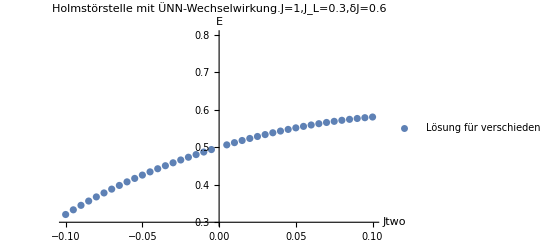

```mathematica
P = ListPlot[{{0.005,0.5061383543970032},{0.01,0.5120545629564276},{0.015,0.5177499419782946},{0.02,0.5232253113491336},{0.025,0.5284810409899552},{0.03,0.5335170949163909},{0.035,0.5383330736651871},{0.04,0.5429282557052943},{0.045,0.5473016383260995},{0.05,0.5514519783756064},{0.055,0.5553778331045751},{0.06,0.5590776012562547},{0.065,0.5625495644324325},{0.07,0.565791928631476},{0.075,0.5688028657857019},{0.08,0.571580554966982},{0.085,0.5741232228756666},{0.09,0.5764291831235824},{0.095,0.5784968737620528},{0.1,0.5803248924608376},{-0.005,0.4936376373090184},{-0.01,0.48704880359280633},{-0.015,0.4802303760534662},{-0.02,0.47317850481841944},{-0.025,0.46588853683788156},{-0.03,0.45835492841246483},{-0.035,0.450571143544755},{-0.04,0.4425295346256594},{-0.045,0.4342212010642832},{-0.05,0.42563582026909474},{-0.055,0.4167614437707956},{-0.06,0.40758424907329094},{-0.065,0.39808823477661004},{-0.07,0.3882548422558306},{-0.075,0.3780624811222856},{-0.08,0.3674859269287972},{-0.085,0.35649554665405064},{-0.09,0.34505628802311406},{-0.095,0.3331263386559427},{-0.1,0.32065531334997005}},AxesLabel->{Jtwo,"E"},PlotLegends->{"Lösung für verschiedene Jtwos"},PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.3,δJ=0.6",PlotRange->{0.3,0.8}]
```

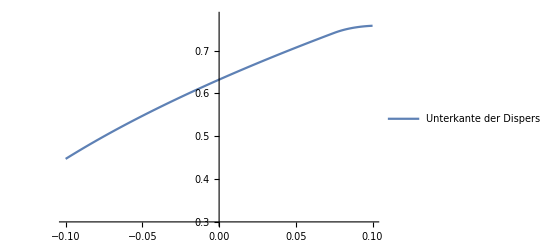

```mathematica
G = Plot[Sqrt[1+2*(0.3*Cos[Inv[0.3,Jtwo]]+Jtwo*Cos[2*Inv[0.3,Jtwo]])],{Jtwo,-0.1,0.1},PlotRange->{0.3,0.78},PlotLegends->{"Unterkante der Dispersion"}]
```

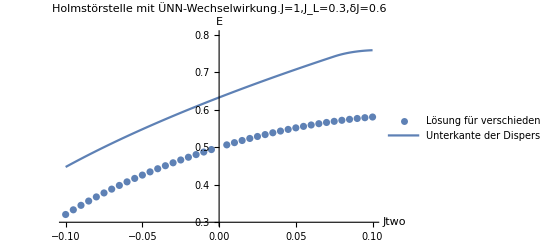

```mathematica
Show[P,G]
```

```mathematica
GLow[J_,Jone_,Jtwo_] := Sqrt[J+2*(Jone*Cos[Inv[Jone,Jtwo]]+Jtwo*Cos[2*Inv[Jone,Jtwo]])]
```

```mathematica
differ[PlusMinus_,Jone_,list_] := Module[{lst = {}},
Do[
Jtwoo = PlusMinus*n*0.005;
AppendTo[lst,{Jtwoo,GLow[1,Jone,Jtwoo]-list[[n,2]]}];
,{n,1,20,1}
];
lst
]
```

```mathematica
differ[-1,0.3,moduler[Lister[-1,-0.005,0.5]]]
```

{{-0.005,0.130862},{-0.01,0.129393},{-0.015,0.128046},{-0.02,0.126821},{-0.025,0.125719},{-0.03,0.12474},{-0.035,0.123885},{-0.04,0.123156},{-0.045,0.122555},{-0.05,0.122087},{-0.055,0.121755},{-0.06,0.121566},{-0.065,0.121527},{-0.07,0.121647},{-0.075,0.121938},{-0.08,0.122412},{-0.085,0.123088},{-0.09,0.123985},{-0.095,0.125131},{-0.1,0.126558}}

```mathematica
differ[1,0.3,moduler[Lister[1,0.005,0.5]]]
```

{{0.005,0.134174},{0.01,0.13602},{0.015,0.137994},{0.02,0.1401},{0.025,0.142339},{0.03,0.144716},{0.035,0.147232},{0.04,0.149892},{0.045,0.152698},{0.05,0.155655},{0.055,0.158765},{0.06,0.162033},{0.065,0.165461},{0.07,0.169055},{0.075,0.754073},{0.08,0.175915},{0.085,0.177737},{0.09,0.178554},{0.095,0.178575},{0.1,0.177963}}

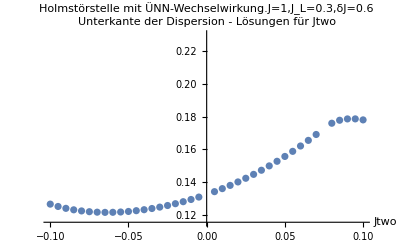

```mathematica
ListPlot[{{-0.005,0.13086216253082145},{-0.01,0.1293925967040913},{-0.015,0.12804587697635572},{-0.02,0.12682149518158053},{-0.025,0.12571944147208003},{-0.03,0.12474026107206526},{-0.035,0.12388512110904792},{-0.04,0.12315589032357871},{-0.045,0.12255523521871903},{-0.05,0.12208673723607144},{-0.055,0.12175503694265488},{-0.06,0.12156601313962723},{-0.065,0.12152700749405321},{-0.07,0.12164710910344789},{-0.075,0.12193751887771442},{-0.08,0.12241202162783837},{-0.085,0.12308760567722127},{-0.09,0.12398528795922886},{-0.095,0.12513123083964123},{-0.1,0.12655828214998782},{0.005,0.13417406934628173},{0.01,0.1360195068843585},{0.015,0.13799391045190545},{0.02,0.1400996467219464},{0.025,0.14233935225998173},{0.03,0.14471590339613594},{0.035,0.1472323863749173},{0.04,0.14989206732225657},{0.045,0.1526983616739005},{0.05,0.15565480281094113},{0.055,0.15876500974970986},{0.06,0.1620326538365432},{0.065,0.1654614244956193},{0.07,0.16905499420347747},{0.075,0.7540727897465934},{0.08,0.1759152644193206},{0.085,0.17773721473696558},{0.09,0.17855426040349254},{0.095,0.17857504801080093},{0.1,0.17796265194431737}},AxesLabel->{Jtwo,"Unterkante der Dispersion - Lösungen für Jtwo"}, PlotLabel->"Holmstörstelle mit ÜNN-Wechselwirkung.J=1,J_L=0.3,δJ=0.6"]
```